```mathematica
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]


GenerateA[N1_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,A[[i,j]]=-ⅈ*Subscript[ω, i],
If[i<j,A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, b,i,j]],
A[[i,j]]=-Subscript[g, j,i]*Exp[ⅈ*Subscript[ϕ, b,j,i]]
];
];
]
];
A
]


GenerateB[N1_,m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,If[m!={}&& IntersectingQ[{i},m],A[[i,j]]=Subscript[ω, i]*Exp[-ⅈ*Subscript[ϕ, s,i]],A[[i,j]]=Subscript[ξ, i]*Exp[-ⅈ*Subscript[ϕ, s,i]]]];
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]],A[[i,j]]=Subscript[χ, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]],A[[i,j]]=Subscript[χ, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]]]];
];
];
A
]

BQH[N1_,m_]:=Module[{A,B,m1,m2,assump},
A=GenerateA[N1];
B=GenerateB[N1,m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=hui∈Reals;
For[i=1,i<=N1,i++,
assump=assump&&Subscript[ω, i]∈Reals&&Subscript[ξ, i]∈Reals&&Subscript[ϕ, s,i]∈Reals;
For[j=i,j<=N1,j++,
If[i!= j,assump=assump&&Subscript[g, i,j]∈Reals&&Subscript[χ, i,j]∈Reals&&Subscript[ϕ, t,i,j]∈Reals&&Subscript[ϕ, b,i,j]∈Reals;]
]];
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

ZeroPhase[Nmodes_]:=Module[{i,j,phases},
phases={};
For[i=1,i<=Nmodes,i++,
phases=phases~Join~{Subscript[ϕ, s,i]->0};
For[j=i,j<=Nmodes,j++,
If[i!= j,phases=phases~Join~{Subscript[ϕ, t,i,j]->0,Subscript[ϕ, b,i,j]->0};]
]];
phases
]

killSPDC[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],(*kill all g_{i,j}*)Flatten@Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}],(*kill all chi except pairwise (2j-1,2j)*)Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

killSPDCBS[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

SPDCBS2[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

(* with a phase *)
SPDCBS3[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->I g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->-I χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];


killomega[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}]];
killxi[N1_]:=Join[Table[Subscript[ξ,i]->0,{i,1,N1}]];
killg[N1_]:=Flatten[Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}]];
killchi[N1_]:=Flatten[Table[Subscript[χ,i,j]->0,{i,1,N1},{j,i+1,N1}]];


CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



QFIperPhoton[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonAnal[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]

QFInoDisp[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/4 (Tr[Σout]-2 Nmodes))//FullSimplify
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(4 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+2 d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]


QFIperPhotonBQH[Nmodes_,EOM_]:=Module[{DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


FnNormal[Nmodes_,g_,χ_,t_]:=Module[{},
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}];
x=Table[((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{k,1,Nmodes},{h,1,Nmodes}];
y=Table[((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{h,1,Nmodes},{k,1,Nmodes}];
tr=Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//N;

nout=1/4 Tr[(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]]-Nmodes/2//N;

Fcov=-1/2 tr-Nmodes;
Fcov/nout
]
```

```mathematica
(* steady-state analytical *)
Clear[ξ1,ω1,κ]
$Assumptions={Subscript[ξ, 1],Subscript[ω, 1],κ}∈Reals;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
"EOM is"
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify;

"DM is"
DM//FullSimplify//MatrixForm

"DM eigenvalues are"
DM//Eigenvalues//FullSimplify

"Stability threshold is"
Solve[-κ/2+√(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)==0,κ]//FullSimplify[Assuming[{Subscript[ξ, 1],Subscript[ω, 1],κ}∈Reals,#]]&
Solve[-κ/2+√(Subscript[ξ, 1]^2-Subscript[ω, 1]^2)==0,Subscript[ω, 1]]//FullSimplify[Assuming[{Subscript[ξ, 1],Subscript[ω, 1],κ}∈Reals,#]]&

"SS covariance matrix"
Σin=LyapunovSolve[DM ,Transpose[DM],-κ IdentityMatrix[2]]//FullSimplify;

Σin//FullSimplify//MatrixForm

"At EP"
Σin/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify//MatrixForm


"Mean photon number is"
n=1/4 (Tr[Σin]- 2 Nmodes)//FullSimplify

"Purity"
μ=1/Sqrt[Det[Σin]]//FullSimplify
"Derivative of purity"
D[μ,Subscript[ω, 1]]//FullSimplify


"QFI w is"
Fw=1/2 1/(1+μ^2)Tr[Inverse[Σin].D[Σin,Subscript[ω, 1]].Inverse[Σin].D[Σin,Subscript[ω, 1]]]+2(D[μ,Subscript[ω, 1]])^2/(1-μ^4)//FullSimplify

"QFI w per photon"
Fwn=Fw/n//FullSimplify
Fwn/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

EOM is

(-κ/2-ⅈ ω_1 | ξ_1
ξ_1 | -κ/2+ⅈ ω_1)

DM is

(-κ/2+ξ_1 | ω_1
-ω_1 | -κ/2-ξ_1)

DM eigenvalues are

{-κ/2-√(ξ_1^2-ω_1^2),-κ/2+√(ξ_1^2-ω_1^2)}

Stability threshold is

{{κ→2 √(ξ_1^2-ω_1^2)}}

{{ω_1→ConditionalExpression[-1/2 √(Im[κ]^2+4 ξ_1^2), Re[κ]==0&&Im[κ]≥0]},{ω_1→ConditionalExpression[1/2 √(Im[κ]^2+4 ξ_1^2), Re[κ]==0&&Im[κ]≥0]},{ω_1→ConditionalExpression[-1/2 √(-κ^2+4 ξ_1^2), κ==Re[κ]&&Re[κ]>0&&(Re[κ]≤2 ξ_1||Re[κ]+2 ξ_1≤0)]},{ω_1→ConditionalExpression[1/2 √(-κ^2+4 ξ_1^2), κ==Re[κ]&&Re[κ]>0&&(Re[κ]≤2 ξ_1||Re[κ]+2 ξ_1≤0)]}}

SS covariance matrix

(1+(2 ξ_1 (κ+2 ξ_1))/(κ^2-4 ξ_1^2+4 ω_1^2) | -(4 ξ_1 ω_1)/(κ^2-4 ξ_1^2+4 ω_1^2)
-(4 ξ_1 ω_1)/(κ^2-4 ξ_1^2+4 ω_1^2) | (κ^2-2 κ ξ_1+4 ω_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2))

At EP

(1+(2 ω_1 (κ+2 ω_1))/κ^2 | -(4 ω_1^2)/κ^2
-(4 ω_1^2)/κ^2 | (κ^2-2 κ ω_1+4 ω_1^2)/κ^2)

Mean photon number is

(2 ξ_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2)

Purity

1/(√(1+(4 ξ_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2)))

Derivative of purity

(16 ξ_1^2 ω_1 √(1+(4 ξ_1^2)/(κ^2-4 ξ_1^2+4 ω_1^2)))/((κ^2+4 ω_1^2)^2)

QFI w is

(8 ξ_1^2 (κ^2-4 ξ_1^2+12 ω_1^2))/((κ^2-4 ξ_1^2+4 ω_1^2)^2 (κ^2-2 ξ_1^2+4 ω_1^2))

QFI w per photon

(4 (κ^2-4 ξ_1^2+12 ω_1^2))/((κ^2-4 ξ_1^2+4 ω_1^2) (κ^2-2 ξ_1^2+4 ω_1^2))

16/κ^2-12/(κ^2+2 ω_1^2)

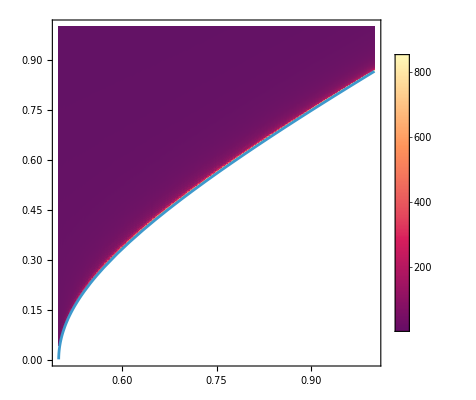

```mathematica
κ=1;
Show[DensityPlot[Fwn,{Subscript[ξ, 1],0.5,1},{Subscript[ω, 1],1/2 √(-κ^2+4 Subscript[ξ, 1]^2),1},PlotPoints->100,PlotLegends->Automatic,PlotRange->All],Plot[1/2 √(-κ^2+4 Subscript[ξ, 1]^2),{Subscript[ξ, 1],0,1}]]
```

```mathematica
(* YOU CAN'T DO THIS, IT MESSES UP THE DERIVATIVE *)

DMEP=DM /.Subscript[ξ, 1]->Subscript[ω, 1]
ΣEP=LyapunovSolve[DMEP,Transpose[DMEP],-κ IdentityMatrix[2]]

"Is solving the Lyapunov equation assuming EP before and after give the same result"
ΣEP==Σin/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify
"Yes, so we have to be differentiating original covariance matrix"
μsq=1/Det[ΣEP]//FullSimplify;
n=1/4 (Tr[ΣEP]- 2 Nmodes)//FullSimplify;
F1=1/2 1/(1+μsq)Tr[Inverse[ΣEP].D[ΣEP,Subscript[ω, 1]].Inverse[ΣEP].D[ΣEP,Subscript[ω, 1]]]//FullSimplify;
F2=1/2 1/(1+μsq)Tr[Inverse[ΣEP].D[Σin,Subscript[ω, 1]].Inverse[ΣEP].D[Σin,Subscript[ω, 1]]]//FullSimplify;
"New expression EP"
FEP=F1/n//FullSimplify
"Old expression at EP"
F2/n/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify//Expand


(*Limit[FEP,κ->∞]*)
```

{{-1/2+ω_1,ω_1},{-ω_1,-1/2-ω_1}}

{{1+2 ω_1+4 ω_1^2,-4 ω_1^2},{-4 ω_1^2,1-2 ω_1+4 ω_1^2}}

Is solving the Lyapunov equation assuming EP before and after give the same result

True

Yes, so we have to be differentiating original covariance matrix

New expression EP

(1+12 ω_1^2)/(ω_1^2+6 ω_1^4+8 ω_1^6)

Old expression at EP

16-28/(1+2 ω_1^2)+16/(1+4 ω_1^2)

1.83303

3.

{-0.0005,-0.0005}

{-1.83353,-0.0005}

{-3.0005,-0.0005}

LIMITS

0

0

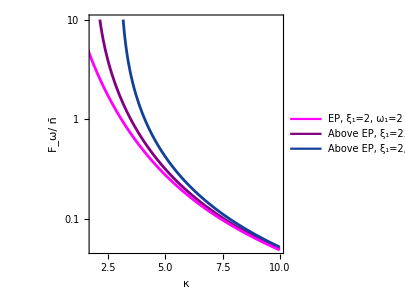

```mathematica
Clear[κ]
EP={Subscript[ξ, 1]->2,Subscript[ω, 1]->2};
aEP1={Subscript[ξ, 1]->2.2,Subscript[ω, 1]->2};
aEP2={Subscript[ξ, 1]->2.5,Subscript[ω, 1]->2};
ϵ=10^-3;
max=10^1;
kmax=10;

th1=2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP1//N
th2=2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]/.aEP2//N

DM/.κ->2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]+ϵ/.EP//Eigenvalues//N
DM/.κ->2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]+ϵ/.aEP1//Eigenvalues//N
DM/.κ->2 Sqrt[Subscript[ξ, 1]^2-Subscript[ω, 1]^2]+ϵ/.aEP2//Eigenvalues//N

"LIMITS"
Limit[Fwn,κ->∞]
Limit[Fwn/.EP,κ->∞]


c2=Show[
LogPlot[{Fwn/.aEP1},{κ,th1+ϵ,kmax},PlotRange->{0,max},PlotStyle->Purple,PlotLegends->Placed[LineLegend[{Magenta,Purple,DarkBlue},{"EP, ξ_1=2, ω_1=2","Above EP, ξ_1=2.2, ω_1=2","Above EP, ξ_1=2, ω_1=1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Top}],GridLinesStyle->LightGray,PlotTheme->"LogGrid",GridLines->Full],
LogPlot[{Fwn/.aEP2},{κ,th2+ϵ,kmax},PlotRange->{0,max},PlotStyle->DarkBlue],
LogPlot[{Fwn/.EP},{κ,0+ϵ,kmax},PlotRange->{0,max},PlotStyle->Magenta
],
Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["κ",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_ω/"Overscript["n","_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300
]
```

```mathematica
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
{{0,-1},{1,0}}.DM//FullSimplify
Σin=MatrixExp[DM t].MatrixExp[Transpose[DM] t]//FullSimplify;
Σin//MatrixForm

"photons nonEP"
n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify
"QFI nonEP"
Fw=1/4 Tr[Inverse[Σin].D[Σin,Subscript[ω, 1]].Inverse[Σin].D[Σin,Subscript[ω, 1]]]//FullSimplify
"QFI per photon nonEP"
Fw/n//FullSimplify

DMep=DM/.Subscript[ξ, 1]->Subscript[ω, 1]
SEP=MatrixExp[DMep t].MatrixExp[Transpose[DMep] t]//FullSimplify//Expand
"QFI EP"


der=t D[DM,Subscript[ω, 1]].MatrixExp[DMep t].MatrixExp[Transpose[DMep] t]+t MatrixExp[DMep t].D[Transpose[DM],Subscript[ω, 1]].MatrixExp[Transpose[DMep] t]//FullSimplify

Inverse[SEP].der.Inverse[SEP].der//FullSimplify
Fwep=1/4 Tr[Inverse[SEP].der.Inverse[SEP].der]//FullSimplify
nep=1/4 (Tr[SEP]-2 Nmodes)//FullSimplify
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

{{ω_1,ξ_1},{ξ_1,ω_1}}

((Cosh[2 t √(ξ_1^2-ω_1^2)] ξ_1^2-ω_1^2+Sinh[2 t √(ξ_1^2-ω_1^2)] ξ_1 √(ξ_1^2-ω_1^2))/(ξ_1^2-ω_1^2) | -(2 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1 ω_1)/(ξ_1^2-ω_1^2)
-(2 Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1 ω_1)/(ξ_1^2-ω_1^2) | -(-Cosh[2 t √(ξ_1^2-ω_1^2)] ξ_1^2+ω_1^2+Sinh[2 t √(ξ_1^2-ω_1^2)] ξ_1 √(ξ_1^2-ω_1^2))/(ξ_1^2-ω_1^2))

photons nonEP

(Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2)/(ξ_1^2-ω_1^2)

QFI nonEP

(2 ξ_1^2 (ξ_1^2 (Sinh[t √(ξ_1^2-ω_1^2)]^4+t^2 ω_1^2)+ω_1^2 (Sinh[t √(ξ_1^2-ω_1^2)]^2-t (t ω_1^2+Sinh[2 t √(ξ_1^2-ω_1^2)] √(ξ_1^2-ω_1^2)))))/((ξ_1^2-ω_1^2)^3)

QFI per photon nonEP

(2 (Sinh[t √(ξ_1^2-ω_1^2)]^2 ξ_1^2+ω_1^2-2 t Coth[t √(ξ_1^2-ω_1^2)] ω_1^2 √(ξ_1^2-ω_1^2)+t^2 Csch[t √(ξ_1^2-ω_1^2)]^2 ω_1^2 (ξ_1^2-ω_1^2)))/((ξ_1^2-ω_1^2)^2)

{{ω_1,ω_1},{-ω_1,-ω_1}}

{{1+2 t ω_1+2 t^2 ω_1^2,-2 t^2 ω_1^2},{-2 t^2 ω_1^2,1-2 t ω_1+2 t^2 ω_1^2}}

QFI EP

{{-2 t^3 ω_1^2,2 t^2 ω_1 (-1+t ω_1)},{-2 t^2 ω_1 (1+t ω_1),2 t^3 ω_1^2}}

{{4 t^4 ω_1^2,0},{0,4 t^4 ω_1^2}}

2 t^4 ω_1^2

t^2 ω_1^2

```mathematica
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
EOM=BQH[Nmodes,{}]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify;

"DM is"
DMep=DM/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify
SEP=MatrixExp[DMep t].MatrixExp[Transpose[DMep] t]//FullSimplify//Expand



der=t D[DM,Subscript[ω, 1]].MatrixExp[DMep t].MatrixExp[Transpose[DMep] t]+t MatrixExp[DMep t].D[Transpose[DM],Subscript[ω, 1]].MatrixExp[Transpose[DMep] t]//FullSimplify

Inverse[SEP].der.Inverse[SEP].der//FullSimplify
"QFI EP"
Fwep=1/4 Tr[Inverse[SEP].der.Inverse[SEP].der]//FullSimplify
nep=1/4 (Tr[SEP]-2 Nmodes)//FullSimplify
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

DM is

{{ω_1,ω_1},{-ω_1,-ω_1}}

{{1+2 t ω_1+2 t^2 ω_1^2,-2 t^2 ω_1^2},{-2 t^2 ω_1^2,1-2 t ω_1+2 t^2 ω_1^2}}

{{-2 t^3 ω_1^2,2 t^2 ω_1 (-1+t ω_1)},{-2 t^2 ω_1 (1+t ω_1),2 t^3 ω_1^2}}

{{4 t^4 ω_1^2,0},{0,4 t^4 ω_1^2}}

QFI EP

2 t^4 ω_1^2

t^2 ω_1^2

```mathematica
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
```

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

DM is

{{-κ/2+ω_1,ω_1},{-ω_1,-κ/2-ω_1}}

{{-2 ⅇ^(-s κ) s^3 κ ω_1^2,2 ⅇ^(-s κ) s^2 κ ω_1 (-1+s ω_1)},{-2 ⅇ^(-s κ) s^2 κ ω_1 (1+s ω_1),2 ⅇ^(-s κ) s^3 κ ω_1^2}}

{{-(2 ⅇ^(-t κ) (-6+6 ⅇ^(t κ)-t κ (6+t κ (3+t κ))) ω_1^2)/κ^3,(2 ⅇ^(-t κ) ω_1 (κ (2-2 ⅇ^(t κ)+t κ (2+t κ))+(-6+6 ⅇ^(t κ)-t κ (6+t κ (3+t κ))) ω_1))/κ^3},{(2 ⅇ^(-t κ) ω_1 (κ (2-2 ⅇ^(t κ)+t κ (2+t κ))+(6-6 ⅇ^(t κ)+t κ (6+t κ (3+t κ))) ω_1))/κ^3,(2 ⅇ^(-t κ) (-6+6 ⅇ^(t κ)-t κ (6+t κ (3+t κ))) ω_1^2)/κ^3}}

{{-(6 ⅇ^(-t κ) (-2+2 ⅇ^(t κ)-t κ (2+t κ)) ω_1^2)/κ^3,(2 ⅇ^(-t κ) ω_1 (2 κ (1-ⅇ^(t κ)+t κ)+(-6+6 ⅇ^(t κ)-3 t κ (2+t κ)) ω_1))/κ^3},{(2 ⅇ^(-t κ) ω_1 (2 κ (1-ⅇ^(t κ)+t κ)+(6-6 ⅇ^(t κ)+3 t κ (2+t κ)) ω_1))/κ^3,(6 ⅇ^(-t κ) (-2+2 ⅇ^(t κ)-t κ (2+t κ)) ω_1^2)/κ^3}}

-((4 ⅇ^(t κ) (ⅇ^(2 t κ) κ^4 (1-ⅇ^(t κ)+t κ)^2-4 κ^2 (1-ⅇ^(t κ)+t κ)^2 (1-ⅇ^(2 t κ)+2 ⅇ^(t κ) t κ) ω_1^2+2 (-2-2 ⅇ^(2 t κ)+t κ (2+t κ)+ⅇ^(t κ) (4+t κ (-2+3 t κ)))^2 ω_1^4))/(κ^2 (1-ⅇ^(t κ)+t κ) (ⅇ^(2 t κ) κ^2+2 (-1+ⅇ^(2 t κ)-2 ⅇ^(t κ) t κ) ω_1^2) (ⅇ^(2 t κ) κ^2+4 (-1+ⅇ^(2 t κ)-2 ⅇ^(t κ) t κ) ω_1^2)))

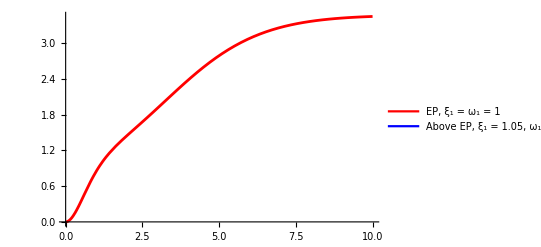

```mathematica
Clear[κ]

(* NOT DIFFERENTIATING THE INTEGRAL CORRECTLY, THERE IS AN INTEGRAL WITHIN AN INTEGRAL *)
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
"DM is"
DMep=DM/.Subscript[ξ, 1]->Subscript[ω, 1]//FullSimplify

integrand=κ s ( D[DM,Subscript[ω, 1]].MatrixExp[DMep s].MatrixExp[Transpose[DMep] s]+ MatrixExp[DMep s].D[Transpose[DM],Subscript[ω, 1]].MatrixExp[Transpose[DMep] s])//FullSimplify
integral=Integrate[integrand,{s,0,t}]

der=t( D[DM,Subscript[ω, 1]].MatrixExp[DMep t].MatrixExp[Transpose[DMep] t]+ MatrixExp[DMep t].D[Transpose[DM],Subscript[ω, 1]].MatrixExp[Transpose[DMep] t])+integral//FullSimplify

S=MatrixExp[DMep t];
Σin= S.Transpose[S]+κ Integrate[ MatrixExp[DMep s].MatrixExp[Transpose[DMep] s],{s,0,t}]//FullSimplify;

tmax=10;

n=1/4 (Tr[Σin]-2 Nmodes)//FullSimplify;
μsq=1/Det[Σin];

Fw=1/(2n) Tr[Inverse[Σin].der.Inverse[Σin].der]/(1+μsq)//FullSimplify

plt1=Plot[{Evaluate[Fw]/.Subscript[ω, 1]->1/.κ->1},{t,0,tmax},PlotRange->All,PlotStyle->Red,PlotLegends->Placed[LineLegend[{Red,Blue},{"EP, ξ_1 = ω_1 = 1","Above EP, ξ_1 = 1.05, ω_1 = 1"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Right,Bottom}]]
```

```mathematica
Limit[Fw/.κ->1/.Subscript[ω, 1]->1//FullSimplify,t->∞]//N
```

3.46667

```mathematica
Limit[Fw/.κ->1/.Subscript[ω, 1]->1//FullSimplify,t->∞]
```

∞

```mathematica
Limit[Fw/.κ->1,t->∞]
```

∞

```mathematica
Limit[Fw/.Subscript[ω, 1]->1,t->∞]
```

∞

```mathematica
Limit[Fw/.ω1->0.9,t->∞]
Fwn/.Subscript[ω, 1]->0.9/.κ->1/.Subscript[ξ, 1]->1
```

(8 ξ_1^2 (-4 ξ_1^2 (κ^2-4 ω_1^2)+(κ^2+4 ω_1^2)^2))/((κ^2+4 ω_1^2) (κ^2-4 ξ_1^2+4 ω_1^2)^2 (κ^2-2 ξ_1^2+4 ω_1^2))

47.2709

```mathematica
(*paper example*)
τz=PauliMatrix[3];
τx=PauliMatrix[1];
Clear[H]
H[δ_,κ_]:=δ τz+ I κ τx;

HEP=H[κ,κ];
Sy=MatrixExp[- I y HEP]//FullSimplify

$Assumptions={δ,y,κ}∈Reals;

cmat=Integrate[
ConjugateTranspose[Sy].τz.D[H[δ,κ],κ].Sy,
{y,0,t}];
cmat//MatrixForm
D[H[δ,κ],κ]
cmat[[1,2]] cmat[[2,1]]//FullSimplify
```

{{1-ⅈ y κ,y κ},{y κ,1+ⅈ y κ}}

(-2/3 t^3 κ^2 | ⅈ t-t^2 κ-2/3 ⅈ t^3 κ^2
-ⅈ t-t^2 κ+2/3 ⅈ t^3 κ^2 | -2/3 t^3 κ^2)

{{0,ⅈ},{ⅈ,0}}

t^2-(t^4 κ^2)/3+(4 t^6 κ^4)/9

```mathematica
Sy=MatrixExp[- I y H[δ,κ]]//FullSimplify
(Cosh[y √(-δ^2+κ^2)]+(ⅈ δ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2)))
```

{{Cosh[y √(-δ^2+κ^2)]-(ⅈ δ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2)),(κ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2))},{(κ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2)),Cosh[y √(-δ^2+κ^2)]+(ⅈ δ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2))}}

```mathematica
Sy=MatrixExp[- I y H[δ,κ]]//FullSimplify
Assuming[δ^2>κ^2&&y∈Reals,FullSimplify[ConjugateTranspose[Sy].τz.D[H[δ,κ],κ].Sy]]
cmat=Integrate[%,{y,0,t}]

cmat[[1,2]] //FullSimplify
cmat[[2,1]]//FullSimplify
```

{{Cosh[y √(-δ^2+κ^2)]-(ⅈ δ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2)),(κ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2))},{(κ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2)),Cosh[y √(-δ^2+κ^2)]+(ⅈ δ Sinh[y √(-δ^2+κ^2)])/(√(-δ^2+κ^2))}}

{{-(2 δ κ Sin[y √(δ^2-κ^2)]^2)/(δ^2-κ^2),(ⅈ (-κ^2+δ^2 Cos[2 y √(δ^2-κ^2)]+ⅈ δ √(δ^2-κ^2) Sin[2 y √(δ^2-κ^2)]))/(δ^2-κ^2)},{(ⅈ (κ^2-δ^2 Cos[2 y √(δ^2-κ^2)]+ⅈ δ √(δ^2-κ^2) Sin[2 y √(δ^2-κ^2)]))/(δ^2-κ^2),-(2 δ κ Sin[y √(δ^2-κ^2)]^2)/(δ^2-κ^2)}}

{{(δ κ (-2 t √(δ^2-κ^2)+Sin[2 t √(δ^2-κ^2)]))/(2 (δ^2-κ^2)^(3/2)),-(δ Sin[t √(δ^2-κ^2)]^2)/(δ^2-κ^2)+1/2 ⅈ ((2 t κ^2)/(-δ^2+κ^2)+(δ^2 Sin[2 t √(δ^2-κ^2)])/((δ^2-κ^2)^(3/2)))},{(ⅈ t κ^2)/(δ^2-κ^2)-(δ Sin[t √(δ^2-κ^2)]^2)/(δ^2-κ^2)-(ⅈ δ^2 Sin[2 t √(δ^2-κ^2)])/(2 (δ^2-κ^2)^(3/2)),(δ κ (-2 t √(δ^2-κ^2)+Sin[2 t √(δ^2-κ^2)]))/(2 (δ^2-κ^2)^(3/2))}}

-(δ Sin[t √(δ^2-κ^2)]^2)/(δ^2-κ^2)+1/2 ⅈ ((2 t κ^2)/(-δ^2+κ^2)+(δ^2 Sin[2 t √(δ^2-κ^2)])/((δ-κ) (δ+κ))^(3/2))

(ⅈ t κ^2)/(δ^2-κ^2)-(δ Sin[t √(δ^2-κ^2)]^2)/(δ^2-κ^2)-(ⅈ δ^2 Sin[2 t √(δ^2-κ^2)])/(2 ((δ-κ) (δ+κ))^(3/2))

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

Eigensystem at EP

{{-κ/2,-κ/2},{{-ⅈ,1},{0,0}}}

Eigensystem

{{-κ/2-√(ξ_1^2-ω_1^2),-κ/2+√(ξ_1^2-ω_1^2)},{{-(ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1},{(-ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1}}}

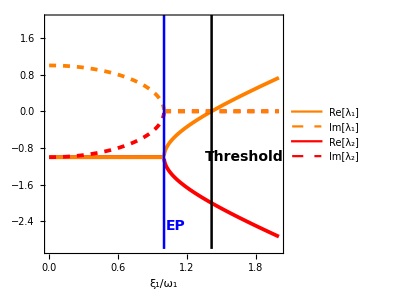

{{-1,-1},{{-ⅈ,1},{0,0}}}

{{-2,0},{{-(ⅈ √(1+ω_1^2))/(ⅈ+ω_1),1},{-(ⅈ √(1+ω_1^2))/(-ⅈ+ω_1),1}}}

√2

```mathematica
Nmodes=1;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify;

"Eigensystem at EP"
Eigensystem[EOM/.Subscript[ξ, 1]->Subscript[ω, 1]]

"Eigensystem "
eig=Eigensystem[EOM]//FullSimplify

κ=2;
c1=Plot[Evaluate[{Re[eig[[1,1]]],Re[eig[[1,2]]],Im[eig[[1,1]]],Im[eig[[1,2]]]}/.Subscript[ω, 1]->1],{Subscript[ξ, 1],0,2},Axes->None,PlotStyle->{{Red,Thickness[0.009]},{Orange,Thickness[0.009]},{Red,Dashed,Thickness[0.009]},{Orange,Dashed,Thickness[0.009]}},Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["ξ_1/ω_1",18,Italic,FontFamily->"Arial"],""},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,PlotLegends->Placed[LineLegend[{Orange,{Orange,Dashed},Red,{Red,Dashed}},{"Re[λ_1]","Im[λ_1]","Re[λ_2]","Im[λ_2]"},LabelStyle->{FontSize->14},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Left,Bottom}],PlotRange->{-3,2},Epilog->{Directive[Blue,Thickness[0.006]],Line[{{1,-3},{1,3}}],Text[Style["EP",14,Blue,FontFamily->"Arial",Bold],{1.1,-2.5}],Directive[Black,Thickness[0.006]],Line[{{Sqrt[2],-3},{Sqrt[2],3}}],Text[Style["Threshold",14,Black,FontFamily->"Arial",Bold],{1.7,-1}]}]

Eigensystem[EOM/.Subscript[ξ, 1]->1/.Subscript[ω, 1]->1]
Eigensystem[EOM/.Subscript[ξ, 1]->1/2 √(κ^2+4 Subscript[ω, 1]^2)]
1/2 √(κ^2+4 Subscript[ω, 1]^2)/.Subscript[ω, 1]->1
```

Unset::norep: Assignment on Subscript for ξ_1 not found.

$Failed

Unset::norep: Assignment on Subscript for ω_1 not found.

$Failed

Eigensystem at EP

{{0,0},{{-ⅈ,1},{0,0}}}

Eigensystem

{{-√(ξ_1^2-ω_1^2),√(ξ_1^2-ω_1^2)},{{-(ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1},{(-ⅈ ω_1+√(ξ_1^2-ω_1^2))/ξ_1,1}}}

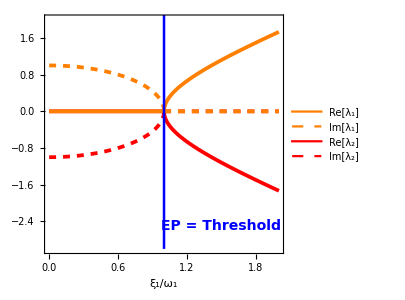

{{0,0},{{-ⅈ,1},{0,0}}}

{{-1,1},{{-(ⅈ √(1+ω_1^2))/(ⅈ+ω_1),1},{-(ⅈ √(1+ω_1^2))/(-ⅈ+ω_1),1}}}

√2

```mathematica
Nmodes=1;
Subscript[ξ, 1]=.
Subscript[ω, 1]=.
Clear[κ]
κ=0;
Nmodes=1;
EOM=BQH[Nmodes,{}]-κ/2 IdentityMatrix[2]/.ZeroPhase[Nmodes];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify;

"Eigensystem at EP"
Eigensystem[EOM/.Subscript[ξ, 1]->Subscript[ω, 1]]

"Eigensystem "
eig=Eigensystem[EOM]//FullSimplify

κ=2;
c3=Plot[Evaluate[{Re[eig[[1,1]]],Re[eig[[1,2]]],Im[eig[[1,1]]],Im[eig[[1,2]]]}/.Subscript[ω, 1]->1],{Subscript[ξ, 1],0,2},Axes->None,PlotStyle->{{Red,Thickness[0.009]},{Orange,Thickness[0.009]},{Red,Dashed,Thickness[0.009]},{Orange,Dashed,Thickness[0.009]}},Frame->True,FrameTicksStyle->Directive[FontSize->15],AspectRatio->1,FrameLabel->{Style["ξ_1/ω_1",18,Italic,FontFamily->"Arial"],""},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,PlotLegends->Placed[LineLegend[{Orange,{Orange,Dashed},Red,{Red,Dashed}},{"Re[λ_1]","Im[λ_1]","Re[λ_2]","Im[λ_2]"},LabelStyle->{FontSize->14},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Left,Bottom}],PlotRange->{-3,2},Epilog->{Directive[Blue,Thickness[0.006]],Line[{{1,-3},{1,3}}],Text[Style["EP = Threshold",14,Blue,FontFamily->"Arial",Bold],{1.5,-2.5}]}]

Eigensystem[EOM/.Subscript[ξ, 1]->1/.Subscript[ω, 1]->1]
Eigensystem[EOM/.Subscript[ξ, 1]->1/2 √(κ^2+4 Subscript[ω, 1]^2)]
1/2 √(κ^2+4 Subscript[ω, 1]^2)/.Subscript[ω, 1]->1
```

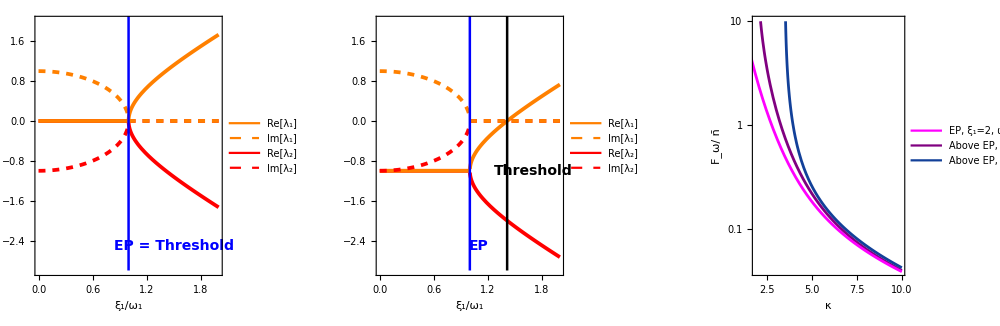

```mathematica
GraphicsRow[{c3,c1,c2},ImageSize->1000]
```